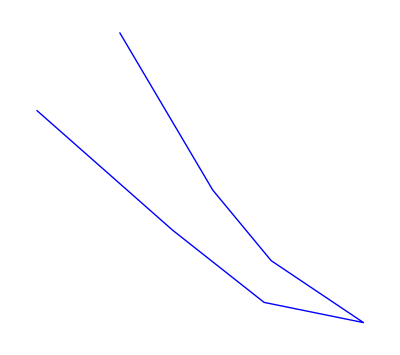
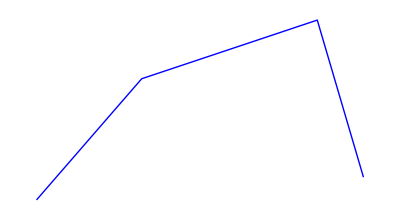
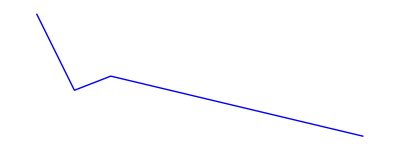
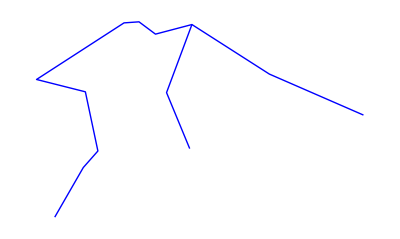
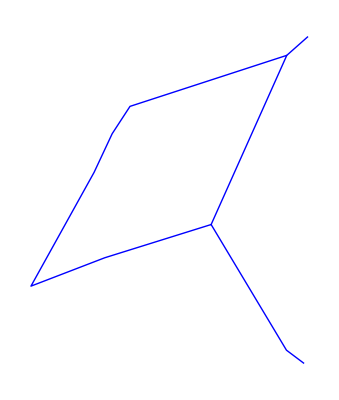
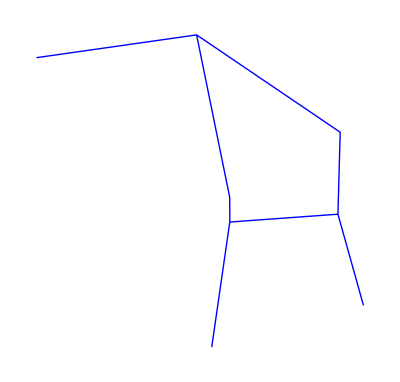
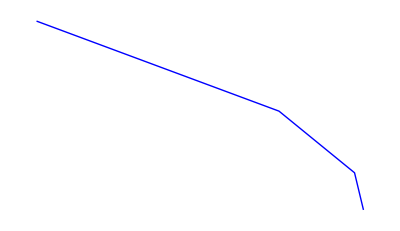
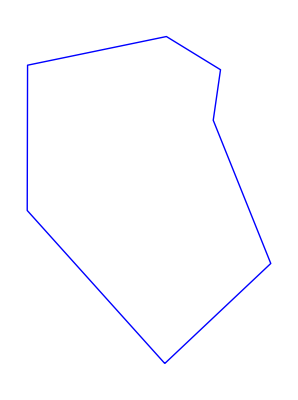
```mathematica
CloudDeploy[
Delayed[
APIFunction[{},
data=RandomSample[{
{"Andromeda (the princess)",-Graphics-},{"Antila (the air pump)",-Graphics-},{"Apus (the bird-of-paradise)",-Graphics-},{"Aquarius (the water-bearer)",-Graphics-},{"Aquila (the eagle)",-Graphics-},{"Ara (the altar)",-Graphics-},{"Aries (the ram)",-Graphics-},{"Auriga (the chariot driver)",-Graphics-},{"Boötes (the herdsman)",-Graphics-},{"Cameleopardalis (the giraffe)",-Graphics-},{"Cancer (the crab)",-Graphics-},{"Canis Major (the bigger dog)",-Graphics-},{"Canis Minor (the smaller dog)",-Graphics-},{"Capricornus (the sea-goat)",-Graphics-},{"Carina (the ship's keel)",-Graphics-},{"Cassiopeia (the queen)",-Graphics-},{"Centaurus (half man, half bull)",-Graphics-},{"Cepheus (the king)",-Graphics-},{"Cetus (the sea monster)",-Graphics-},{"Chamaeleon",-Graphics-},{"Columbia (the dove)",-Graphics-},{"Corona Australis (the southern crown)",-Graphics-},{"Corona Borealis (the northern crown)",-Graphics-},{"Corvus (the crow)",-Graphics-},{"Crater (the cup)",-Graphics-},{"Crux (the cross)",-Graphics-},{"Cygnus (the swan)",-Graphics-},{"Delphinus (the dolphin)",-Graphics-},{"Dorado (the swordfish)",-Graphics-},{"Draco (the dragon)",-Graphics-},{"Equuleus (the pony)",-Graphics-},{"Eridanus (the river)",-Graphics-},{"Gemini (the twins)",-Graphics-},{"Grus (the crane)",-Graphics-},{"Hercules",-Graphics-},{"Horologium (the pendulum clock)",-Graphics-},{"Hydra (many-headed serpent)",-Graphics-},{"Hydrus (water-snake)",-Graphics-},{"Indus (the Native American)",-Graphics-},{"Lacerta (the lizard)",-Graphics-},{"Leo (the lion)",-Graphics-},{"Lepis (the hare)",-Graphics-},{"Libra (the balance scales)",-Graphics-},{"Lupus (the wolf)",-Graphics-},{"Lynx",-Graphics-},{"Lyra (the lyre)",-Graphics-},{"Mensa (the table)",-Graphics-},{"Monoceros (the unicorn)",-Graphics-},{"Musca (the fly)",-Graphics-},{"Norma (the carpenter's level)",-Graphics-},{"Ophiuchus (the serpent-bearer)",-Graphics-},{"Orion (the hunter)",-Graphics-},{"Pavo (the peacock)",-Graphics-},{"Pegasus (the flying horse)",-Graphics-},{"Perseus (a Greek demigod)",-Graphics-},{"Phoenix (the bird born of fire)",-Graphics-},{"Pisces (the fishes)",-Graphics-},{"Piscis Austrinus (the southern fish)",-Graphics-},{"Puppis (the poop deck)",-Graphics-},{"Sagitta (the arrow)",-Graphics-},{"Sagittarius (the archer)",-Graphics-},{"Scorpius (the scorpion)",-Graphics-},{"Sculptor",-Graphics-},{"Serpens (the snake)",-Graphics-},{"Taurus (the bull)",-Graphics-},{"Tucana (the toucan)",-Graphics-},{"Ursa Major (the great bear)",-Graphics-},{"Ursa Minor (the smaller bear)",-Graphics-},{"Vela (the sails)",-Graphics-},{"Virgo (the maiden)",-Graphics-},{"Volans (the flying fish)",-Graphics-}},4];
choices=#[[1]]&/@data;
mixed=RandomSample[choices];
ans=Position[mixed,choices[[1]]][[1,1]];
q=Style["This is the shape produced by connecting the stars in one of these constellations. Which one?",TextAlignment->Center];
pic=data[[1,2]];
InputForm[{q,ans,mixed,Append[pic,ImageSize->{{480},{540}}]}]&]],
"CS_pack_Astr6",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/user-4dec8a61-25b0-47e1-8624-e5b3610139af/CS_pack_Astr6]